## Equations

```mathematica
Ycon[l_,m_,θp_,ϕp_]:=(-1)^-m SphericalHarmonicY[l,-m,θp,ϕp]
```

```mathematica
σ[θp_]:=Sin[θp]
```

```mathematica
σnew[θp_,ϕp_]:=∑_(l=0)^15 ∑_(m=-l)^l (SphericalHarmonicY[l,m,θp,ϕp] ∫_0^(2 π) ∫_0^π Sin[θp] Ycon[l,m,θp,ϕp]σ[θp] ⅆθpⅆϕp)
```

```mathematica
σnew[θp,ϕp]//FullSimplify
```

$Aborted

```mathematica
(SphericalHarmonicY[l,m,θp,ϕp] ∫_0^(2 π) ∫_0^π Sin[θp] Ycon[l,m,θp,ϕp]σ[θp] ⅆθpⅆϕp)/.{l-> 1,m-> 1}
```

$Aborted

```mathematica
Table[∫_0^(2 π) ∫_0^π Sin[θp] Ycon[l,m,θp,ϕp]σ[θp] ⅆθpⅆϕp,{l,0,6},{m,-l,l}]//MatrixForm
```

({π^(3/2)/2}
{0,0,0}
{0,0,-1/16 √5 π^(3/2),0,0}
{0,0,0,0,0,0,0}
{0,0,0,0,-(3 π^(3/2))/128,0,0,0,0}
{0,0,0,0,0,0,0,0,0,0,0}
{0,0,0,0,0,0,-(5 √13 π^(3/2))/2048,0,0,0,0,0,0})

```mathematica
Table[∫_0^(2 π) ∫_0^π Sin[θp] Ycon[l,m,θp,ϕp]σ[θp] ⅆθpⅆϕp,{l,7,10},{m,-l,l}]//MatrixForm
```

({0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
{0,0,0,0,0,0,0,0,-(35 √17 π^(3/2))/32768,0,0,0,0,0,0,0,0}
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
{0,0,0,0,0,0,0,0,0,0,-(147 √21 π^(3/2))/262144,0,0,0,0,0,0,0,0,0,0})

```mathematica
Table[∫_0^(2 π) ∫_0^π Sin[θp] Ycon[l,m,θp,ϕp]σ[θp] ⅆθpⅆϕp,{l,11,12},{m,-l,l}]//MatrixForm
```

({0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
{0,0,0,0,0,0,0,0,0,0,0,0,-(3465 π^(3/2))/2097152,0,0,0,0,0,0,0,0,0,0,0,0})

```mathematica
∫_0^(2 π) ∫_0^π Sin[θp] Ycon[1,0,θp,ϕp]σ[θp] ⅆθpⅆϕp
```

(p √(3/π))/(2 a^3)

```mathematica
G[θp_,ϕp_,θ_,ϕ_,rb_,rs_]:=4 π ∑_(l=0)^3 ∑_(m=-l)^l 1/(2 l+1)Ycon[l,m,θp,ϕp] SphericalHarmonicY[l,m,θ,ϕ] rs^l/rb^(l+1)
```

```mathematica
Pot[θp_,ϕp_,θ_,ϕ_,rb_,rs_]:=1/(4 π ϵ0) ∫_0^(2 π) ∫_0^π Sin[θp] G[θp,ϕp,θ,ϕ,rb,rs] a^2  σnew[θp,ϕp] ⅆθpⅆϕp
```

```mathematica
Pot[θp,ϕp,θ,ϕ,rbig,rsm]
```

(p rsm Cos[θ] (7 rbig^2-3 rsm^2+5 rsm^2 Cos[θ]^2))/(28 a π rbig^4 ϵ0)

```mathematica
(p rsm Cos[θ] (7 rbig^2-3 rsm^2+5 rsm^2 Cos[θ]^2))/(28 a π rbig^4 ϵ0)/.{rsm->rs,rbig->rb}
```

(p rs Cos[θ] (7 rb^2-3 rs^2+5 rs^2 Cos[θ]^2))/(28 a π rb^4 ϵ0)

```mathematica
(p r_< Cos[θ] (7 (r_>)^2-3 (r_<)^2+5 (r_<)^2 Cos[θ]^2))/(28 a π (r_>)^4 ϵ0)
```

## Plots

```mathematica
σnew[θp,ϕp]
```

(3 p Cos[θp])/(4 a^3 π)+(p (-3 Cos[θp]+5 Cos[θp]^3))/(4 a^3 π)

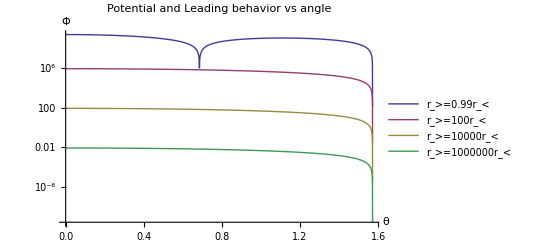

```mathematica
rs=a;
a=1;
p=1;
rb=1.01; 
LogPlot[{Abs[(p rs Cos[θ])/(4 a π rb^2 ϵ0)-(p rs Cos[θ] (7 rb^2-3 rs^2+5 rs^2 Cos[θ]^2))/(28 a π rb^4 ϵ0)],Abs[(p rs Cos[θ])/(4 a π (100 rb)^2 ϵ0)-(p rs Cos[θ] (7 rb^2-3 rs^2+5 rs^2 Cos[θ]^2))/(28 a π (100 rb)^4 ϵ0)],Abs[(p rs Cos[θ])/(4 a π (10000 rb)^2 ϵ0)-(p rs Cos[θ] (7 rb^2-3 rs^2+5 rs^2 Cos[θ]^2))/(28 a π (10000 rb)^4 ϵ0)],Abs[(p rs Cos[θ])/(4 a π (1000000 rb)^2 ϵ0)-(p rs Cos[θ] (7 rb^2-3 rs^2+5 rs^2 Cos[θ]^2))/(28 a π (1000000 rb)^4 ϵ0)]},{θ,0,π/2},PlotLegends->{"r_>=0.99r_<","r_>=100r_<","r_>=10000r_<","r_>=1000000r_<"},AxesLabel->{"θ","Φ"},PlotLabel-> "Potential and Leading behavior vs angle",PlotRange->All]
```

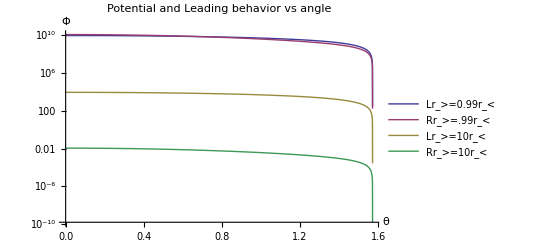

```mathematica
rs=.99;
 ϵ0
a=1;
p=1;
rb=1.01; 
LogPlot[{(p rs Cos[θ])/(4 a π rb^2 ϵ0),(p rs Cos[θ] (7 rb^2-3 rs^2+5 rs^2 Cos[θ]^2))/(28 a π rb^4 ϵ0),(p rs Cos[θ])/(4 a π (1000 rb)^2 ϵ0),(p rs Cos[θ] (7 rb^2-3 rs^2+5 rs^2 Cos[θ]^2))/(28 a π (1000 rb)^4 ϵ0)},{θ,0,π/2},PlotLegends->{"Lr_>=0.99r_<","Rr_>=.99r_<","Lr_>=10r_<","Rr_>=10r_<"},AxesLabel->{"θ","Φ"},PlotLabel-> "Potential and Leading behavior vs angle"]
```

```mathematica
diffDiv[θ_,rb_]:=Abs[((p Cos[θ])/(4 a π rb^2 ϵ0)-(p rs Cos[θ] (7 rb^2-3 rs^2+5 rs^2 Cos[θ]^2))/(28 a π rb^4 ϵ0))]/Abs[(p rs Cos[θ] (7 rb^2-3 rs^2+5 rs^2 Cos[θ]^2))/(28 a π rb^4 ϵ0)] 100
```

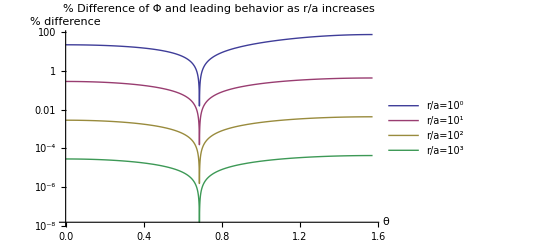

```mathematica
rs=1;
 ϵ0=8.85 10^-12;
a=1;
p=1;
rb=1; 
LogPlot[{diffDiv[θ,rb],diffDiv[θ,10^1 rb],diffDiv[θ,10^2 rb],diffDiv[θ,10^3 rb]},{θ,0,π/2},PlotLegends->{"r/a=10^0","r/a=10^1","r/a=10^2","r/a=10^3"},AxesLabel->{"θ","% difference"},PlotLabel-> "% Difference of Φ and leading behavior as r/a increases",PlotRange->All]
```

## Junk

```mathematica
Pot[θp,ϕp,θ,ϕ]//Expand
```

5.13321×10^9 Cos[θ]+5.98879×10^9 Cos[θ]^3

```mathematica
Pot[θp,ϕp,θ,ϕ,rb,rs]
```

```mathematica
(p rs Cos[θ] (7 rb^2-3 rs^2+5 rs^2 Cos[θ]^2))/(28 a π rb^4 ϵ0)//Expand
```

(5 p rs^3 Cos[θ]^3)/(28 π a rb^4 ϵ0)-(3 p rs^3 Cos[θ])/(28 π a rb^4 ϵ0)+(p rs Cos[θ])/(4 π a rb^2 ϵ0)

```mathematica
Limit[Pot[θp,ϕp,θ,ϕ,rb,1],rb->10^6 a]//N//Expand
```

-(5.68411×10^-27 p Cos[θ])/(a^5 ϵ0)+(7.95775×10^-14 p Cos[θ])/(a^3 ϵ0)+(2.84205×10^-26 p Cos[θ] Cos[2. θ])/(a^5 ϵ0)

```mathematica
diffDiv[π/4,rb]
```

6.14102

```mathematica
?? Series
```

Series[f,{x,x_0,n}] generates a power series expansion for f about the point x=x_0 to order (x-x_0)^n. 
Series[f,{x,x_0,n_x},{y,y_0,n_y},…] successively finds series expansions with respect to x, then y, etc.

Attributes[Series]={Protected}
 
Options[Series]:={Analytic→True,Assumptions:>$Assumptions}

```mathematica
Series[(p rs Cos[θ] (7 rb^2-3 rs^2+5 rs^2 Cos[θ]^2))/(28 a π rb^4 ϵ0),{rb,0,15}]//FullSimplify
```

(p rs^3 Cos[θ] (-1+5 Cos[2 θ]))/(56 a π ϵ0 rb^4)+(p rs Cos[θ])/(4 a π ϵ0 rb^2)+O[rb]^16

```mathematica
(p rs Cos[θ] (7 rb^2-3 rs^2+5 rs^2 Cos[θ]^2))/(28 a π rb^4 ϵ0)//FullSimplify
```

(p rs Cos[θ] (7 rb^2-3 rs^2+5 rs^2 Cos[θ]^2))/(28 a π rb^4 ϵ0)